## Hydrodynamic & Rigid moments of inertia

### The Hydrodynamic moments of inertia in Lund convention: with minus (-) in the sine function

```mathematica
moiHM[γ_,k_,i0_]:=4/3 i0*Sin[γ-(2π)/3*k]^2;
```

### The Hydrodynamic moments of inertia in Lund convention: with plus (+) in the sine function

```mathematica
moiHP[γ_,k_,i0_]:=4/3 i0*Sin[γ+(2π)/3*k]^2;
```

### The Rigid moments of inertia in Lund convention with minus (-) in the cosine function

```mathematica
moiRigM[β_,γ_,k_,i0_]:=i0/(1+(5/(16π))^(1/2)β)(1-(5/(4π))^(1/2)β*Cos[γ-(2π)/3*k]);
```

### The Rigid moments of inertia in Lund convention with minus (+) in the cosine function

```mathematica
moiRigP[β_,γ_,k_,i0_]:=i0/(1+(5/(16π))^(1/2)β)(1-(5/(4π))^(1/2)β*Cos[γ+(2π)/3*k]);
```

### The nuclear radius in terms of the deformation parameters

```mathematica
rk[β_,γ_,k_]:=r0*(1+(5/(4π))^(1/2)β*Cos[γ+(2π)/3*k]);
```

```mathematica
rad[xdeg_]:=xdeg*π/180;
```

## Graphical representations

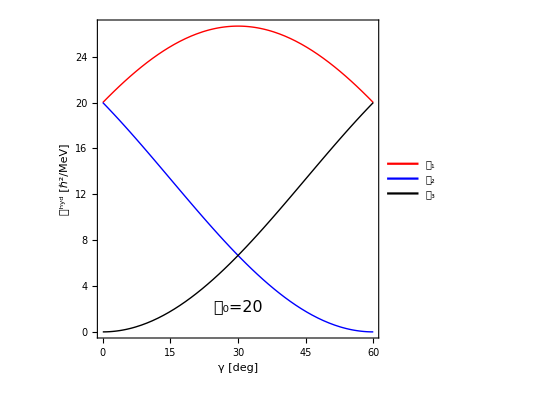

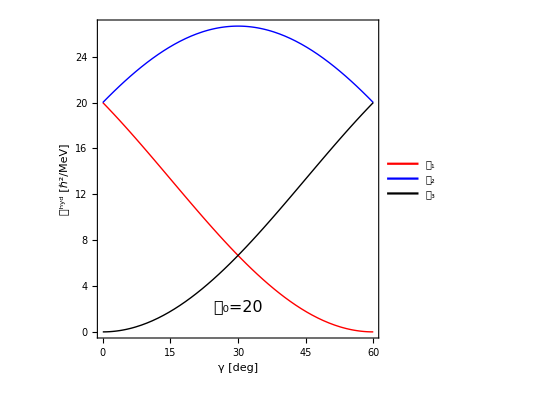

```mathematica
mois[MOI_,left_,right_,i0_]:=Plot[{MOI[rad[x],1,i0],MOI[rad[x],2,i0],MOI[rad[x],3,i0]},{x,left,right},Frame->True,Axes->False,AspectRatio->1,FrameLabel->{Style["γ [deg]",Italic],Style["𝒥^hyd [ℏ^2/MeV]",Italic]},FrameStyle->Directive[Thick,Black],LabelStyle->{16,FontFamily->"Menlo",Black},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Thick}},PlotLegends->Placed[{Style["𝒥_1",Red],Style["𝒥_2",Blue],Style["𝒥_3",Black]},{0.2,0.3}],Epilog->Inset[Style[StringTemplate["𝒥_0=``"][i0],16,Black,FontFamily->"Menlo"],Scaled[{0.5,0.1}]]];
Show[mois[moiHM,0,60,20]]
Show[mois[moiHP,0,60,20]]
```